A notebook for some other fit files that (as Arie) proved to be less good than the one Yoav did

## 18.fit

124.

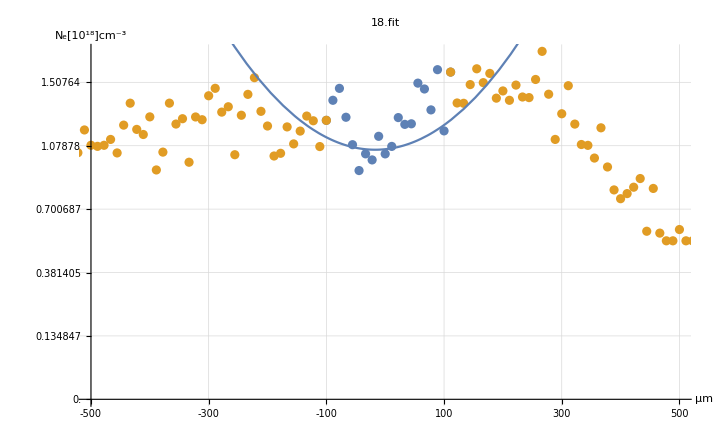

```mathematica
data=Import["C:\\Users\\HILL\\MEGASync\\msc\\measurements\\rdp\\data from fig files.xlsx",{"Dataset",1},HeaderLines->1];
line=Normal[data[All,"line"]];
fwhm=t=Normal[data[All,"fwhm"]];
range=Normal[data[All,"exclude indices (from to)"]]⟦1;;2⟧;start=range⟦1⟧;end=range⟦2⟧; (*center of parabola is at indice 9 of the range i.e., line⟦9+76⟧=124*)
center=line⟦9+76⟧
(*the plot range is 45 lines to the right and to the left from the center, beacuse the capillary extends over 90 rows in the verical dimension *)
width=90;
parabola=p1 x^2+p2 x+p3/.{p1->0.07022, p2->-17.2,p3->1132};
Show[{
ListPlot[{
Thread[{line⟦start;;end⟧,fwhm⟦start;;end⟧}]
,
Thread[{Join[line⟦;;start⟧,line⟦end;;⟧],Join[fwhm⟦;;start⟧,fwhm⟦end;;⟧]}]
}
,PlotRange->{{center-width/2,center+width/2},Automatic}
],
Plot[parabola,{x,center-45,center+45}]
}
,Ticks->{Thread[{
Subdivide[center-width/2,center+width/2,10]
,
Subdivide[-500,500,10]
}], Thread[{
Subdivide[0,100,5]
,
(Subdivide[0,100,5]/5.4*0.071)^(3/2)
}]}
,TicksStyle->Large
,GridLines->Automatic
,PlotLabel->Style["18.fit",20]
,AxesLabel->{Style["  μm",FontSize->30],Style["N_e[10^18]cm^-3",FontSize->30]}
,ImageSize->720]
```

## 19.fit

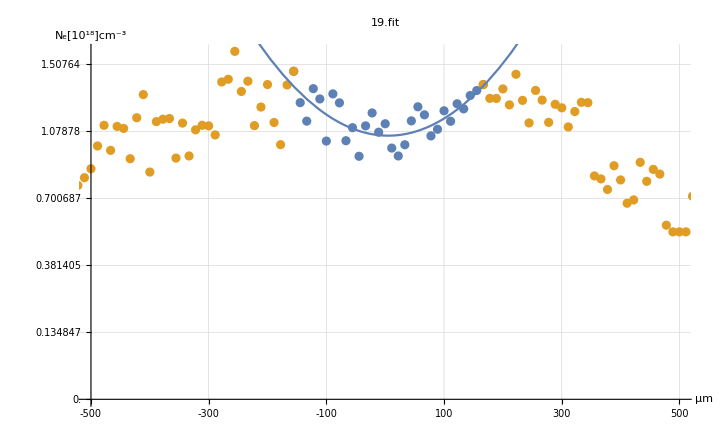

```mathematica
data=Import["C:\\Users\\HILL\\MEGASync\\msc\\measurements\\rdp\\data from fig files.xlsx",{"Dataset",2},HeaderLines->1];
line=Normal[data[All,"line"]];
fwhm=t=Normal[data[All,"fwhm"]];
range=Normal[data[All,"exclude indices (from to)"]]⟦1;;2⟧;start=range⟦1⟧;end=range⟦2⟧; (*center of parabola is at indice 9 of the range i.e., line⟦9+76⟧=124*)
center=line⟦69+14⟧;
(*the plot range is 45 lines to the right and to the left from the center, beacuse the capillary extends over 90 rows in the verical dimension *)
width=90;
parabola=p1 x^2+p2 x+p3/.{p1->0.07022, p2->-17.2,p3->1132};
Show[{
ListPlot[{
Thread[{line⟦start;;end⟧,fwhm⟦start;;end⟧}]
,
Thread[{Join[line⟦;;start⟧,line⟦end;;⟧],Join[fwhm⟦;;start⟧,fwhm⟦end;;⟧]}]
}
,PlotRange->{{center-width/2,center+width/2},Automatic}
],
Plot[parabola,{x,center-45,center+45}]
}
,Ticks->{Thread[{
Subdivide[center-width/2,center+width/2,10]
,
Subdivide[-500,500,10]
}], Thread[{
Subdivide[0,100,5]
,
(Subdivide[0,100,5]/5.4*0.071)^(3/2)
}]}
,TicksStyle->Large
,GridLines->Automatic
,PlotLabel->Style["19.fit",20]
,AxesLabel->{Style["  μm",FontSize->30],Style["N_e[10^18]cm^-3",FontSize->30]}
,ImageSize->720]
```